```mathematica
P[τ_] :=1/2*(A*Exp[-a* τ]+ C*Exp[-c* τ]*Sin[Ω*τ + Θ]);
ns = 10^-9;
MHz = 10^6;
(*η = 0;*)
Γ1 =  1/(10ns);
Γ0 = 0;
Subscript[γ, 10] = 0;
Subscript[γ, ϕ]= 1/(20 ns);
Γp=Γ1+Γ0;
Γ = 1/2(Γ1+Γ0+ Subscript[γ, 10]) + Subscript[γ, ϕ];
Subscript[a, 1]= 1/2 Γp;
Subscript[c, 1] = 1/4(2Γ + (Γp + 2 Subscript[γ, 10]));

varParams = {A -> 1,Ω-> 800 MHz,a -> Subscript[a, 1],C -> 1,c->Subscript[c, 1], Θ -> -1.6, Subscript[η, e] -> 1};
plt1 = Plot[{P[τ] /. varParams}, {τ,0,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

-Graphics-

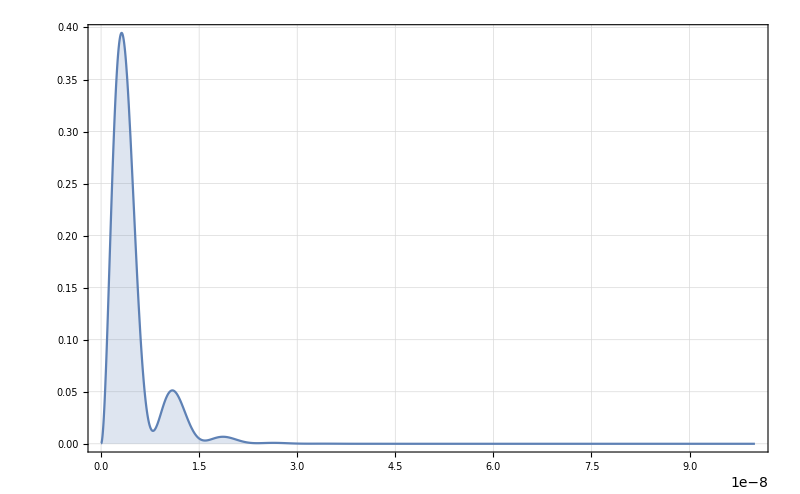

```mathematica
Pnorm1 = Integrate[P[τ],{τ, 0, ∞}];
P2a =Integrate[P[t]*P[τ - t], {t, 0, τ}];
Pnorm2 = Pnorm1^2;
P2at[τ_] =P2a;
P3a =Integrate[P2at[t]*P[τ - t], {t, 0, τ}];
Pnorm3 = Pnorm1^3;
P3at[τ_] =P3a;
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

```mathematica
(*P4a =Integrate[P3at[t]*P[τ - t], {t, 0, τ}];
Pnorm4 = Pnorm1^4;
P4at[τ_] =P4a;*)
```

```mathematica
(*P4at[τ_] =P4a;
P5a =Integrate[P4at[t]*P[τ - t], {t, 0, τ}];
Pnorm5 = Pnorm1^5;
P5at[τ_] =P5a;
P6a =Integrate[P5at[t]*P[τ - t], {t, 0, τ}];
Pnorm6 = Pnorm1^6;
P6at[τ_] =P6a;
P7a =Integrate[P6at[t]*P[τ - t], {t, 0, τ}];
Pnorm7 = Pnorm1^7;*)
(*P7at[τ_] =P7a;*)
(*Save["P2a.m",P2a]
Save["P3ra.m",P3a]
Save["P4a.m",P4a]*)
(*Save["P5ra.m",P5a]
Save["P6a.m",P6a]
Save["P7ra.m",P7a]*)
(*Save["Pnorm1.m",Pnorm1]
Save["Pnorm2.m",Pnorm2]
Save["Pnorm3.m",Pnorm3]

Save["Pnorm4.m",Pnorm4]*)
(*Save["Pnorm5.m",Pnorm5]
Save["Pnorm6.m",Pnorm6]
Save["Pnorm7.m",Pnorm7]*)
```

```mathematica
varParams = {A -> 1,Ω-> 800 MHz,a -> Subscript[a, 1],C -> 1,c->Subscript[c, 1], Θ -> -1.6};
pltM = Plot[{P[τ]/ Pnorm1 /. varParams}, {P2at[τ]/Pnorm2  + P3at[τ]/Pnorm3 /. varParams}, {τ,0,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

Plot::nonopt: Options expected (instead of {τ,0,100 ns}) beyond position 2 in Plot[{P[τ]/Pnorm1/.varParams},{P2at[τ]/Pnorm2+P3at[τ]/Pnorm3/.varParams},{τ,0,100 ns},PlotRange→All,Frame→True,GridLines→Automatic,ImageSize→800,PlotPoints→100,Filling→0]. An option must be a rule or a list of rules.

Plot[{P[τ]/Pnorm1/.varParams},{P2at[τ]/Pnorm2+P3at[τ]/Pnorm3/.varParams},{τ,0,100 ns},PlotRange→All,Frame→True,GridLines→Automatic,ImageSize→800,PlotPoints→100,Filling→0]

```mathematica
Pint1[τ_, T_] := Integrate[P[t],{t, τ, T}]
```

```mathematica
Pint21[τ_, T_] := NIntegrate[P2at[t]/P[t] /. varParams,{t, τ, T}]
```

```mathematica
D1[τ_, η_] := η*Binomial[1,1]*P[τ]/Pnorm1 + η*(1- η)*Binomial[2,1] *P2at[τ]/Pnorm2 + η*(1- η)^2*Binomial[3, 1]*P3at[τ]/Pnorm3

D2[τ_, η_] := η^2*Binomial[2,2]*P2at[τ]/Pnorm2 + η^2*(1- η)*Binomial[3,2] *P3at[τ]/Pnorm3
Dint21[τ_, T_,η_]:= NIntegrate[D2[t, η]/D1[t, η] /. varParams,{t, τ, T}]
```

```mathematica
Pint21[10ns, 100ns]
```

2.60854×10^-15

```mathematica
A = Pnorm1/Pnorm2 /. varParams
```

NIntegrate::levmaxord: -1.54717×10^17 ⅇ^(-50000000 t) t+«13»+((Cos[1600000000 t]+ⅈ Sin[1600000000 t]) ((-4.47965×10^18+2.16118×10^17 ⅈ) (1/16 ⅇ^(-75000000 t) Cos[800000000 t]-1/16 ⅈ ⅇ^(-75000000 t) Sin[800000000 t])+640625000000000000 (-100000000 ⅇ^(-75000000 t) t Cos[1.6+Times[«2»]]+100000000 ⅈ ⅇ^(-75000000 t) t Sin[1.6+Times[«2»]])))/800000000 is a Levin function of differential order 172 which exceeds value of option "MaxOrder" -> 50. Treating -1.54717×10^17 ⅇ^(-50000000 t) t+«13»+((Cos[1600000000 t]+ⅈ Sin[1600000000 t]) ((-4.47965×10^18+2.16118×10^17 ⅈ) (1/16 ⅇ^(-75000000 t) Cos[800000000 t]-1/16 ⅈ ⅇ^(-75000000 t) Sin[800000000 t])+640625000000000000 (-100000000 ⅇ^(-75000000 t) t Cos[1.6+Times[«2»]]+100000000 ⅈ ⅇ^(-75000000 t) t Sin[1.6+Times[«2»]])))/800000000 as a non-Levin function.

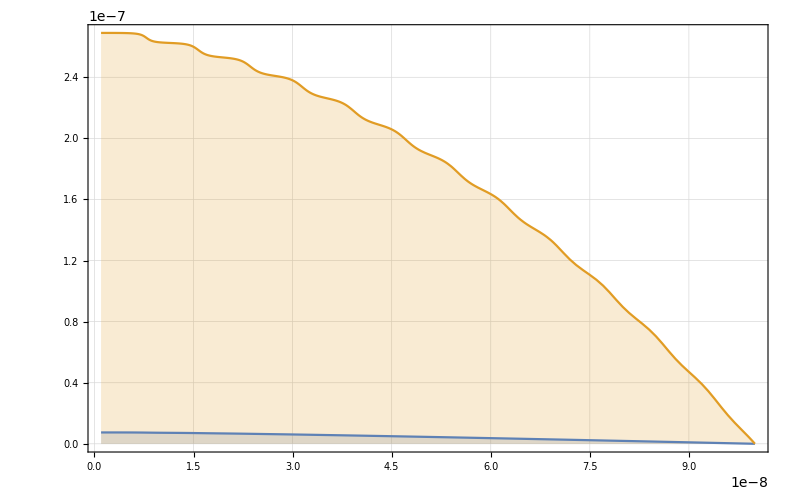

```mathematica
pltM = Plot[{{Dint21[τ, 100ns, 0.1] },{Dint21[τ, 100ns, 1] }}, {τ,1 ns,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

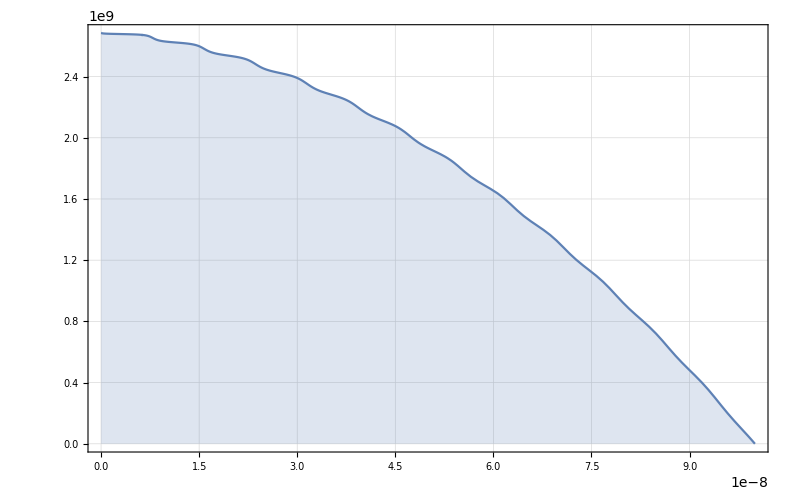

```mathematica
pltM = Plot[{Pint21[τ, 100ns] *A }, {τ,0,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

```mathematica
(*Subscript[D, 2]^(1)[τ_] := *)
```

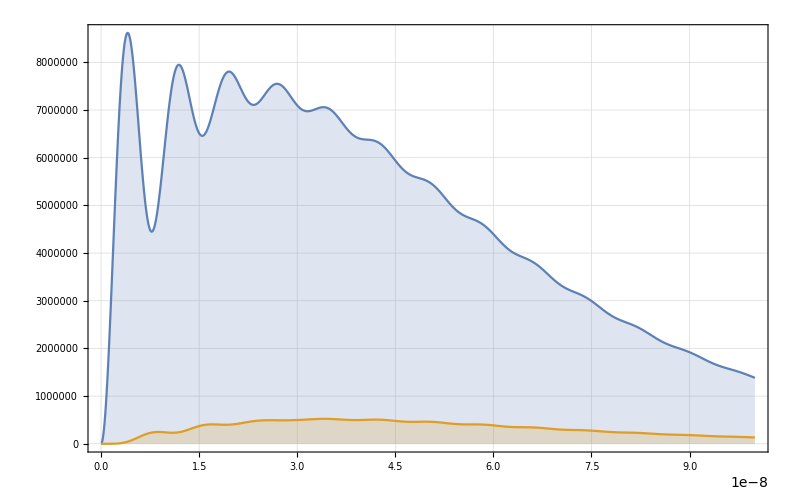

```mathematica
varParams = {A -> 1,Ω-> 800 MHz,a -> Subscript[a, 1],C -> 1,c->Subscript[c, 1], Θ -> -1.6};
pltM = Plot[{{D1[τ, 0.1]/. varParams}, {D1[τ,0.1]/. varParams}}, {τ,0,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

```mathematica
norm[η_,M_, K_, Η_]:=Simplify[Sum[Binomial[n,M]*Η^n*η^M*(1 - η)^(n - M), {n, M, K}]]
```

norm

```mathematica
Simplify[Sum[Sum[Binomial[n,M]*Η^n*η^M*(1 - η)^(n - M), {n, 1, 100}], {M, 1, 100}]]
```

η Η (1-(-2+η) Η+144+(147+η^98) Η^98-(-100+4950 η-161700 η^2+3921225 η^3-75287520 η^4+1192052400 η^5-16007560800 η^6+186087894300 η^7-1902231808400 η^8+17310309456440 η^9-141629804643600 η^10+1050421051106700 η^11-7110542499799200 η^12+44186942677323600 η^13-253338471349988640 η^14+1345860629046814650 η^15-6650134872937201800 η^16+30664510802988208300 η^17-132341572939212267400 η^18+535983370403809682970 η^19-2041841411062132125600 η^20+87+535983370403809682970 η^79-132341572939212267400 η^80+30664510802988208300 η^81-6650134872937201800 η^82+1345860629046814650 η^83-253338471349988640 η^84+44186942677323600 η^85-7110542499799200 η^86+1050421051106700 η^87-141629804643600 η^88+17310309456440 η^89-1902231808400 η^90+186087894300 η^91-16007560800 η^92+1192052400 η^93-75287520 η^94+3921225 η^95-161700 η^96+4950 η^97-100 η^98+η^99) Η^99)
 |  |  |  |

```mathematica
Derivative[Simplify[Sum[Binomial[n,M]*Η^n*η^M*(1 - η)^(n - M), {n, M, ∞}]], η]
```

```mathematica
Derivative[η^M Η^M (1+(-1+η) Η)^(-1-M),η]
```

Derivative[η^M Η^M (1+(-1+η) Η)^(-1-M),η]

```mathematica
D[η Η (1+(-1+η) Η)^(-1-1),η]
```

-(2 η Η^2)/(1+(-1+η) Η)^3+Η/(1+(-1+η) Η)^2

```mathematica
Refine[Abs[η]> 0&& Abs[Η]>0]
```

Abs[η]>0&&Abs[Η]>0

```mathematica
row=Function[ Simplify[Sum[Binomial[n,#]*Η^n*η^#*(1 - η)^(n - #), {n, #, ∞}]] ]
```

Simplify[∑_(n=#1)^∞ Binomial[n,#1] Η^n η^#1 (1-η)^(n-#1)]&

```mathematica
.00
```

```mathematica
row[2]
```

(η^2 Η^2)/(1+(-1+η) Η)^3

```mathematica
Sum[Binomial[n,M]*η^n*(1 - η)^(M - n), {n, 0, M}]
```

-(-1+η)^M (-1+2 η)^(-1-M) (-η^M+η^(1+M)+((η (-1+2 η))/(-1+η))^M-2 η ((η (-1+2 η))/(-1+η))^M+(1-2 η)^(1+M) Binomial[0,M] Hypergeometric2F1[1,1,1-M,-η/(-1+η)])

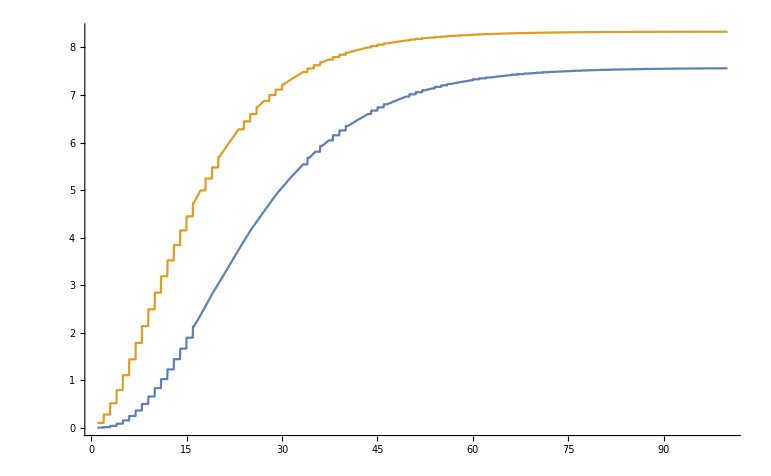

```mathematica
Plot[{{norm[0.1, 2, K, 0.99]}, {norm[0.1, 1, K, 0.99]}},{K, 1, 100}, PlotRange-> All]
```

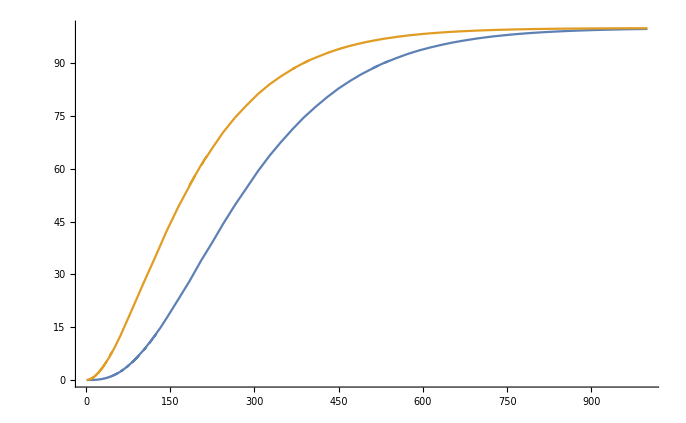

```mathematica
Plot[{{norm[0.01, 2, K, 1]}, {norm[0.01, 1, K, 1]}},{K, 1, 1000}, PlotRange-> All]
```

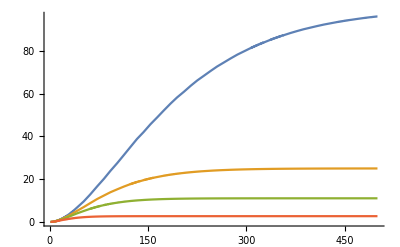

```mathematica
Plot[{{norm[0.01, 1, K, 1]}, {norm[0.01, 1, K, 0.99]}, {norm[0.01, 1, K, 0.98]}, {norm[0.01, 1, K, 0.95]}},{K, 1, 500}, PlotRange-> All]
```

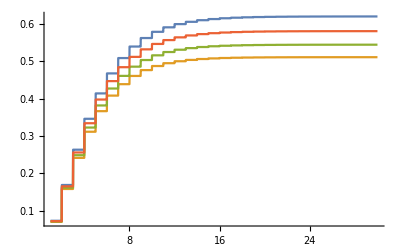

```mathematica
Plot[{{norm[0.1, 1, K, 0.73]}, {norm[0.1, 1, K, 0.70]}, {norm[0.1, 1, K, 0.71]}, {norm[0.1, 1, K, 0.72]}},{K, 1, 30}, PlotRange-> All]
```

```mathematica
Plot[{{norm[0.1, 1, K, 0.7]}, {norm[0.15, 1, K, 0.70]}},{K, 1, 30}, PlotRange-> All]
```

-Graphics-

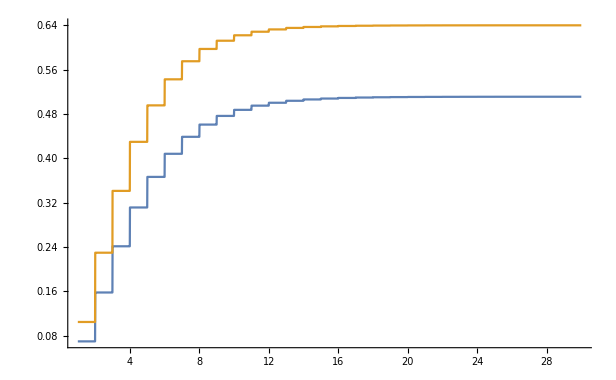
```mathematica
-Graphics--Graphics-
```

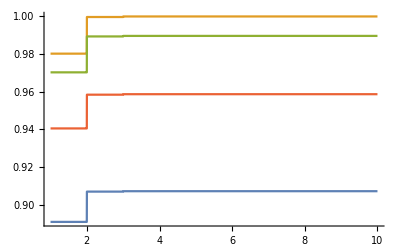

```mathematica
Plot[{{norm[0.99, 1, K, 0.9]}, {norm[0.99, 1, K, 0.99]}, {norm[0.99, 1, K, 0.98]}, {norm[0.99, 1, K, 0.95]}},{K, 1, 10}, PlotRange-> All]
```

```mathematica
Sum[η^n,{n, 1, ∞}]
```

-η/(-1+η)

```mathematica
D12 [τ_, T_] := (D1[τ] * Integrate[D1[t],{t, τ, T}])/Integrate[D2[t],{t, 0, T}]
```

```mathematica
D1 = NIntegrate[D1[t, 100 ns] /. varParams, {t, 0, 100ns}]
```

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1/10000000}}.

$Aborted

```mathematica
Integrate[D1[t]]
```

```mathematica
Plot[{D12[τ, 100ns]/. varParams}, {τ,1ns,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

NIntegrate::inumr: The integrand D1[t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.001×10^-9,1/10000000}}.

NIntegrate::inumr: The integrand D2[t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1/10000000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

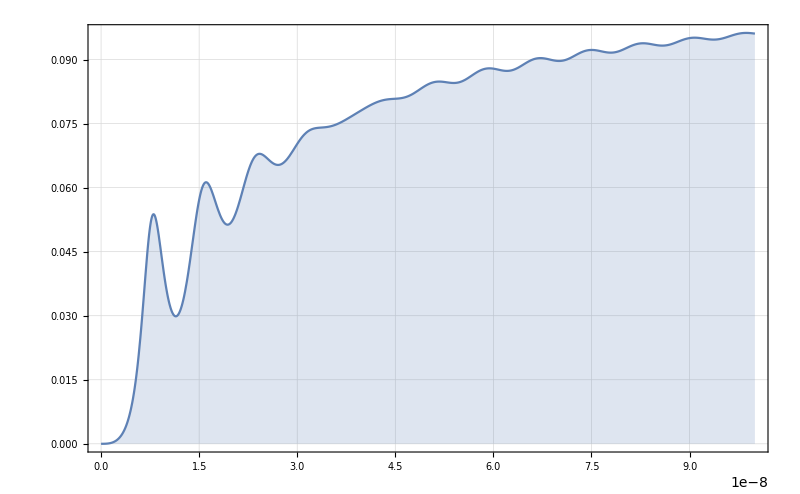

```mathematica
Plot[{{D2[τ, 0.1]/D1[τ,0.1]/. varParams}(*, {D2[τ, 1]/D1[τ,1]/. varParams}*)}, {τ,0,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

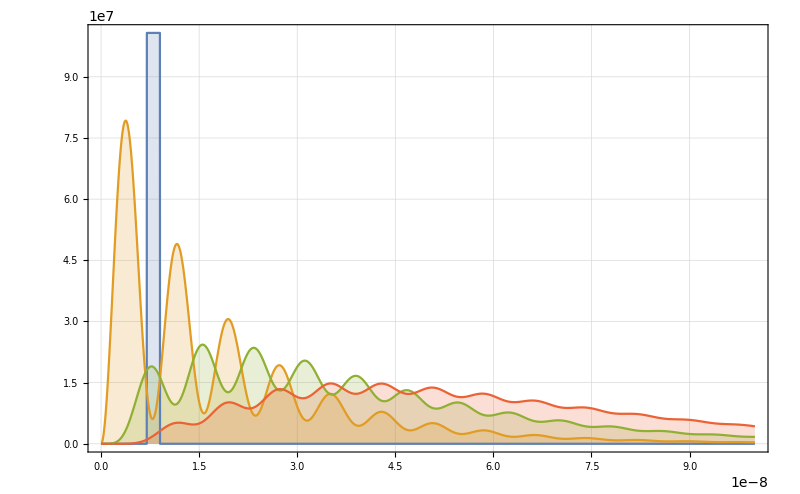

```mathematica
pltM = Plot[{{UnitStep[(1 ns)/ns - ((τ - 8ns)/ns)^2]/Pnorm1 /. varParams},{P[τ]/ Pnorm1 /. varParams}, {P2at[τ]/ Pnorm2/. varParams}, {P3at[τ]/ Pnorm3/. varParams}}, {τ,0,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

```mathematica
binWidth = 0.5ns;
```

```mathematica
Pbin1 = Table[NIntegrate[P[t]*UnitStep[binWidth/ns - ((τ - t)/ns)^2] /. varParams, {t,0 ns, 20ns }], {τ, 0ns, 20ns, 0.5ns}];
Pbin2 = Table[NIntegrate[P2at[t]*UnitStep[binWidth/ns - ((τ - t)/ns)^2] /. varParams, {t,0 ns, 20ns }], {τ, 0ns, 20ns, 0.5ns}];
Pbin3 = Table[ NIntegrate[P3at[t]*UnitStep[binWidth/ns - ((τ - t)/ns)^2] /. varParams, {t,0 ns, 20ns }], {τ, 0ns, 20ns, 0.5ns}];
```

```mathematica
ListPlot[{Pbin1/Pnorm1 , Pbin2/Pnorm2} /.varParams]
```

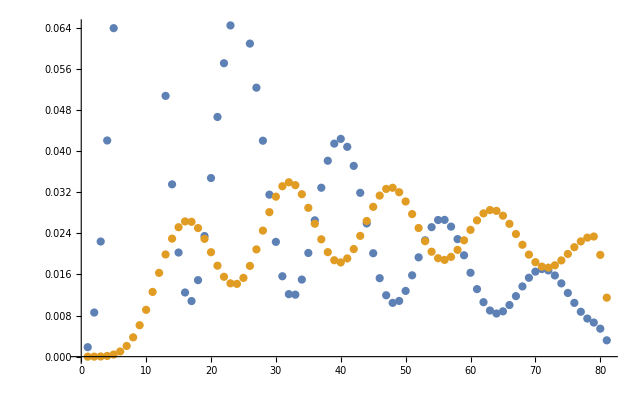

-Graphics-

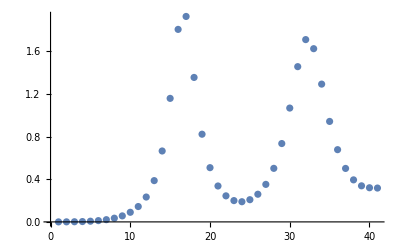

```mathematica
ListPlot[ (Pbin2/Pnorm2)/(Pbin1/Pnorm1  + Pbin3/Pnorm3) /.varParams]
```

```mathematica
g20= (2Pbin2/Pnorm2 + 6Pbin3/Pnorm3)/(Pbin1/Pnorm1 + 2Pbin2/Pnorm2 + 3Pbin3/Pnorm3)^2;
(*g20a= (2Pbin2/Pnorm2)/(Pbin1/Pnorm1 + 2Pbin2/Pnorm2)^2;*)
```

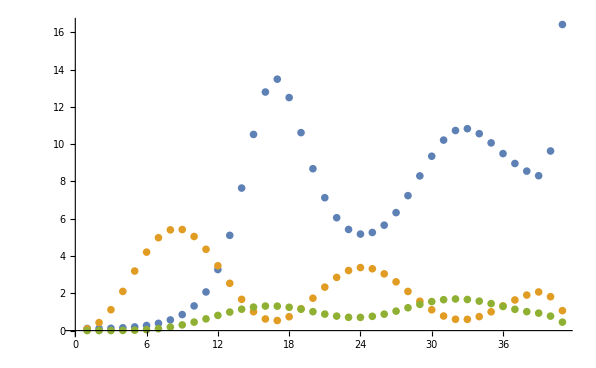

```mathematica
varParams= {A -> 1,Ω-> 800 MHz,a -> Subscript[a, 1],C -> 1,c->Subscript[c, 1], Θ -> -1.6};
(*ListPlot[  /. varParams, PlotRange->1]*)
ListPlot[{g20, 50*Pbin1/Pnorm1 , 50*Pbin2/Pnorm2} /.varParams]
```

```mathematica
|
```

```mathematica
etaSolved = Simplify[Solve[(Subscript[D, 2]^2(1 - η))/(Subscript[D, 1]- Subscript[D, 2])^2 + Subscript[D, 2]/(Subscript[D, 1]- Subscript[D, 2])(2 - T/Subscript[D, 1] - 2η) + η - 1==0, η]]
```

{{η→(D_1^3-4 D_1^2 D_2-T D_2^2+D_1 D_2 (T+2 D_2))/(D_1 (D_1^2-4 D_1 D_2+2 D_2^2))}}

```mathematica
Refine[ T* Subscript[D, 2]*(Subscript[D, 1] - Subscript[D, 2]) < -Subscript[D, 1] *(Subscript[D, 1]^2-4 Subscript[D, 1] *Subscript[D, 2]+2 Subscript[D, 2]^2), T - Subscript[D, 2]- Subscript[D, 1] > 0 && T > 0 && Subscript[D, 2]>0 && Subscript[D, 1]>0]
```

T (D_1-D_2) D_2<-D_1 (D_1^2-4 D_1 D_2+2 D_2^2)

```mathematica
(Subscript[D, 1]^3-4 Subscript[D, 1]^2 Subscript[D, 2]-T Subscript[D, 2]^2+Subscript[D, 1] Subscript[D, 2] (T+2 Subscript[D, 2]))/(Subscript[D, 1] (Subscript[D, 1]^2-4 Subscript[D, 1] Subscript[D, 2]+2 Subscript[D, 2]^2))
TrueQ[Simplify[Solve[(Subscript[D, 2]^2(1 - η))/(Subscript[D, 1]- Subscript[D, 2])^2 + Subscript[D, 2]/(Subscript[D, 1]- Subscript[D, 2])(2 - T/Subscript[D, 1] - 2η) + η - 1==0, η]]]
```

(D_1^3-4 D_1^2 D_2-T D_2^2+D_1 D_2 (T+2 D_2))/(D_1 (D_1^2-4 D_1 D_2+2 D_2^2))

False